```mathematica
eps0=8.85418781762039*10^-12;
k=1/eps0/4/Pi;
rp=4.445*10^-6;
rho=1500;
m=4.0/3.0*Pi*rp^3*rho;
gamma= 4.341689383904344*m;

aw=3.03731419*10^6;
cw=1.14352594*10^6;
kappa=-3.84037247*10^10;
r0=0.0016622715189364113;
zw=3.80913378*10^(-1)*r0;
qw=9.64691720*10^-15;
qtop=-3.105494829523742*10^-15;
qbot=-2.589789085330693*10^-15;
(*zbot = 0.002742747106163061;
ztop = 0.0032248049595676263;*)
zbot =0.0027886618943559704;
ztop = 0.0031863724551996647;

trap=-1035598;

eqRtop=0.00034015213;
eqRbot=0.00012685477;
eqOmega=60;
eqPhi =  1.471;
```

```mathematica
(**)
ebotRad = {1, 0,0};
ebotTau = {0, 1,0};
etopRad = {Cos[dPhi], Sin[dPhi],0};
etopTau = {-Sin[dPhi], Cos[dPhi], 0}; 
(**)
rbotVec = {rbot, 0,zbot};
rtopVec = {rtop * Cos[dPhi], rtop*Sin[dPhi], ztop}; 
dist = Norm[rtopVec-rbotVec];
(**)
fbt = k*qtop*qbot/dist^3*(rtopVec-rbotVec); 

coeff=Exp[
-aw*Norm[{rbotVec[[1]]-rtopVec[[1]], rbotVec[[2]]-rtopVec[[2]]}]^2 
-cw*(-rbotVec[[3]]+rtopVec[[3]]-zw)^2
]; 
ftb=- fbt+coeff*qbot*k*qw/r0*
{
2*aw*(rbotVec[[1]]-rtopVec[[1]]), 
2*aw*(rbotVec[[2]]-rtopVec[[2]]),
2*cw*(-rbotVec[[3]]+rtopVec[[3]]-zw)
};
(**)
fbtRad = Dot[fbt, etopRad];
fbtTau = Dot[fbt, etopTau];
ftbRad = Dot[ftb, ebotRad];
ftbTau = Dot[ftb, ebotTau];
(**)
```

```mathematica
(**)
eqns = {
fbtTau/rtop-ftbTau/rbot==0, 
1/2/gamma*(fbtTau/rtop+ftbTau/rbot)==Omega, 
rtop*(qtop*trap-m*Omega^2)==fbtRad, 
rbot*(qbot*trap-m*Omega^2)==ftbRad
};
initgss={{rtop, eqRtop}, {rbot,eqRbot}, {Omega,eqOmega},{dPhi,eqPhi}};
(**)
sol=FindRoot[eqns,initgss, MaxIterations->10000]
(**)
```

{rtop→0.000341939,rbot→0.00010035,Omega→60.,dPhi→1.471}

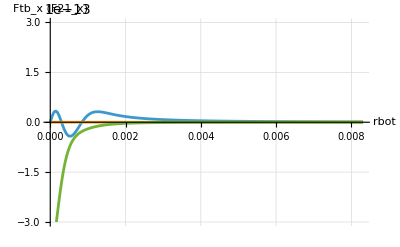

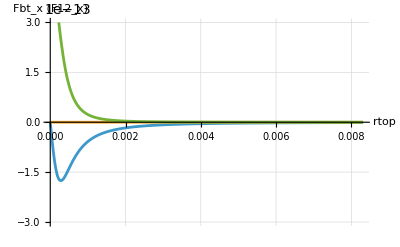

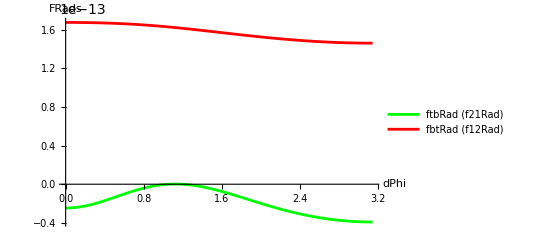

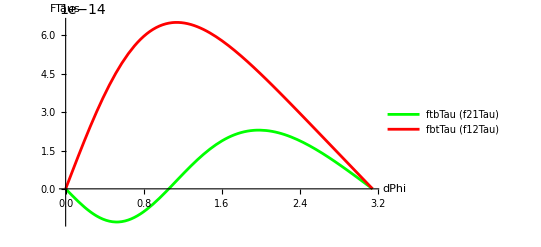

```mathematica
Plot[{ftb[[1]] /. {rtop->0,  dPhi->Pi}, ftb[[2]] /. {rtop->0,  dPhi->Pi},ftb[[3]] /. {rtop->0,  dPhi->Pi} }, {rbot, 0, r0*5}, AxesLabel->{"rbot", "Ftb_x (F21_x)"}, PlotRange->{Automatic,{-3*10^-13,3*10^-13}},GridLines->Automatic]
(**)
Plot[{fbt[[1]] /. {rtop->0,  dPhi->Pi}, fbt[[2]] /. {rtop->0,  dPhi->Pi},fbt[[3]] /. {rtop->0,  dPhi->Pi}}, {rbot, 0, r0*5}, AxesLabel->{"rtop", "Fbt_x (F12_x)"},PlotRange->{Automatic,{-3*10^-13,3*10^-13}},GridLines->Automatic]
(**)
Plot[{ftbRad /. {rtop->eqRtop, rbot->eqRbot}, fbtRad /. {rtop->eqRtop, rbot->eqRbot}}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "FRads"}, PlotLegends->{"ftbRad (f21Rad)", "fbtRad (f12Rad)"}, PlotStyle->{Green, Red}]
Plot[{ftbTau /. {rtop->eqRtop, rbot->eqRbot}, fbtTau /. {rtop->eqRtop, rbot->eqRbot}}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "FTaus"},  PlotLegends->{"ftbTau (f21Tau)", "fbtTau (f12Tau)"}, PlotStyle->{Green, Red}]
```